# Лабораторная работа №10

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр . Ковалевская В . С .
    10 ноября 2021

## Задание 2.1

Создать в Mathematica подсистему для работы с точкой
на плоскости : спроектировать внутреннее представление объекта «точка на плоскости», реализовать способы задания объекта, возможности извлечения его свойств, построения графического образа .

### Задание 2.1

Спроектируйте в Mathematica внутреннее представление объекта
«точка на плоскости» .

```mathematica
kmPoint[km, id_String, coord: {_,_}](*координаты точки в прямоугольной декартовой системе координат на плоскости*)
```

kmPoint[km,id_String,coord:{_,_}]

### Задание 2.3

Создайте конструктор объекта «точка на плоскости», требующий
указания ее декартовых координат (прямоугольная декартова система координат) .

```mathematica
ClearAll[kmPoint];
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord];
```

```mathematica
kmPoint[{1,2}]
```

kmPoint[km,,{1,2}]

### Задание 2.4

Создайте возможность задания объекта «точка» путем указания ее имени и декартовых координат (прямоугольная декартова система координат) .

```mathematica
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord];
```

```mathematica
kmPoint["A",{1,2}]
```

kmPoint[km,A,{1,2}]

```mathematica
myP=kmPoint["моя Точка",{1,0}]
```

kmPoint[km,моя Точка,{1,0}]

### Задание 2.5

Создайте возможность задания объекта «точка на плоскости»
посредством указания ее полярных координат (согласованных с прямоугольной декартовой системой координат) .

```mathematica
kmPoint[{∅_,ρ_},"pol"]:=kmPoint[km,"",{ρ Cos[∅],ρ Sin[∅]}];
```

```mathematica
kmPoint[{π/3,2},"pol"]
```

kmPoint[km,,{1,√3}]

### Задание 2.6

Создайте возможность задания объекта «точка» посредством указания ее полярных координат (согласованных с прямоугольной декартовой системой координат) и, возможно, имени точки .

```mathematica
kmPoint[id___String,{∅_,ρ_},"pol"]:=kmPoint[km,id,{ρ Cos[∅],ρ Sin[∅]}];
```

```mathematica
kmPoint["A",{π/3,2},"pol"]
```

kmPoint[km,A,{1,√3}]

## Задание 2.2

Свойства геометрического объекта «точка на плоскости»

### Задание 2.7

```mathematica
kmPoint[km, id_String,___]["id"]:=If[id=="","Точка",id];
```

```mathematica
kmPoint["A",{1,2}]["id"]
```

A

```mathematica
myP["id"]
```

моя Точка

```mathematica
kmPoint[{5,2}]["id"]
```

Точка

```mathematica
kmPoint[{π/3,2},"pol"]["id"]
```

Точка

### Задание 2.8

Напишите оператор, возвращающий декартовы координаты заданного объекта «точка на плоскости» .

```mathematica
kmPoint[km,_String,coord_List,___]["coord"]:=coord;
```

```mathematica
kmPoint[{π/3,2},"pol"]["coord"]
```

{1,√3}

```mathematica
myP["coord"]
```

{1,0}

### Задание 2.9

Постройте булеву функцию, позволяющую определить, имеет ли представленный объект «точка на плоскости» имя .

```mathematica
NamedQ[kmPoint[km,id_String,___]]^:=id≠"";
```

```mathematica
?kmPoint
```

```mathematica
NamedQ[myP]
```

True

```mathematica
NamedQ[kmPoint[{π/3,2},"pol"]]
```

False

## Задание 2.3

Отображение точки на рисунке

### Задание 2.10

Три точки P1, P2, P3, заданные в прямоугольной декартовой системе координат соответственно координатами (−1, 0), (5, 3), (−2, 2) . Представьте точки P1, P2, P3 в Mathematica, каждую как экземпляр объекта «точка на плоскости», и отобразите представленные точки в графической области.

```mathematica
{P1,P2,P3}=kmPoint/@{{-1,0},{5,3},{-2,2}}
```

{kmPoint[km,,{-1,0}],kmPoint[km,,{5,3}],kmPoint[km,,{-2,2}]}

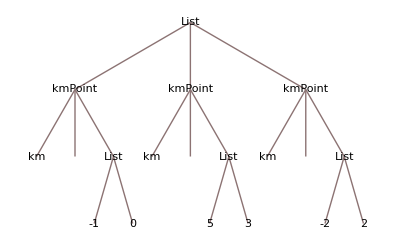

```mathematica
{P1,P2,P3}//TreeForm
```

```mathematica
#["coord"]&/@{P1,P2,P3}(*Извлечем координаты из представления каждой точки формируя запрос”coord” о свойствах объекта «точка на плоскости»*)
```

{{-1,0},{5,3},{-2,2}}

```mathematica
Point/@(#["coord"]&/@{P1,P2,P3})
```

{Point[{-1,0}],Point[{5,3}],Point[{-2,2}]}

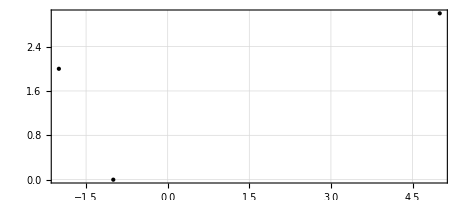

```mathematica
Graphics[Point/@(#["coord"]&/@{P1,P2,P3}),Frame->True,GridLines->Automatic]
```

```mathematica
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[Point/@(#["coord"]&/@gp),opts];
```

```mathematica
kmGraphics2D[{P1,P2,P3},Frame->True,GridLines->Automatic]
```

-Graphics-